```mathematica
(*realnoise=Import["~/p/tg/realnoise.csv","CSV"];
imagnoise=Import["~/p/tg/imagnoise.csv","CSV"];
noise=realnoise+imagnoise*ⅈ;
r=Length[noise];*)
r=128;
noise=Fourier@RandomComplex[{-1-I,1+I},{r,r}];
For[x=1,x<=r,x++,
For[y=1,y≤r,y++,
d=EuclideanDistance[{x,y},{r/2-.5,r/2-.5}]/r;
noise[[x,y]]=nf@d*noise[[x,y]];
]
]
```

```mathematica
ifourier=InverseFourier@noise;
{ImageAdjust@Image@Log@Abs@noise,ImageAdjust@Image@Abs@Re@ifourier,ReliefImage@Abs@ifourier}
```

{-Graphics-,-Graphics-,-Graphics-}

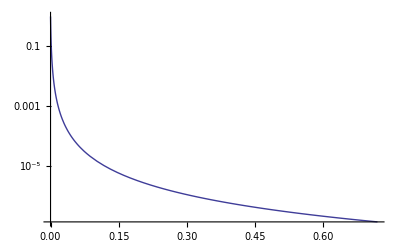

```mathematica
nf[d_]:=(1/(1000d+1))^2.4
LogPlot[nf[d],{d,0,.72},PlotRange->Full]
```